```mathematica
(* 3D Plot of Binomial Coefficients*)
Manipulate[Plot3D[Binomial[x,y],{x,0,maxX},{y,0,x},PlotStyle->Opacity[0.8],AxesLabel->{"x (Degree)","y (Coefficient)","\[Binomial]x, y"},PlotRange->All,MeshFunctions->{#1&,#2&},ColorFunction->"Rainbow"],{{maxX,10},1,20,1},(*Slider for maximum degree x*)SaveDefinitions->True]
```

```mathematica
(* 2D Pascal's Triangle Plot*)
Manipulate[ArrayPlot[Table[Binomial[i,j],{i,0,x},{j,0,i}],Frame->True,ColorFunction->"Rainbow",PlotLabel->Style["Pascal's Triangle up to Degree x = "<>ToString[x],Bold],FrameTicks->{Range[0,x],Automatic}],{{x,5},1,200,1},(*Slider for degree x*)SaveDefinitions->True]
```

```mathematica
(* Plot Binomial Coefficients for Fixed 𝑥 *)
Manipulate[ListPlot[Table[{y,Binomial[x,y]},{y,0,x}],Joined->False,PlotStyle->{Blue,PointSize[Large]},Filling->Axis,(*Adds vertical lines to the axis*)AxesOrigin->{0,0},(*Ensures the axes start at zero*)Frame->True,(*Adds frame for better appearance*)FrameLabel->{"Degree","Coefficient"},(*Proper labels*)PlotRange->All,GridLines->Automatic,(*Adds grid lines for better readability*)PlotLabel->Style["Binomial Coefficients for Degree x = "<>ToString[x],Bold,16]],{{x,20},1,36,1},(*Slider for degree x,matching graph range*)SaveDefinitions->True]
```

```mathematica
(* Binomial coeff VS. Normal distribution, Binomial Distribution well-approximate a normal distribution *)
Manipulate[Module[{data,mean,stddev,norm},data=Table[Binomial[x,y],{y,0,x}];
mean=x/2;(*Mean*)stddev=Sqrt[x/4];(*Standard Deviation*)norm=Table[Max[data]*PDF[NormalDistribution[mean,stddev],y],{y,0,x}];
ListPlot[{data,norm},Joined->{False,True},PlotStyle->{{Blue,PointSize[Medium]},{Red,Dashed}},PlotLegends->{"Binomial Coefficients","Normal Approximation"},Frame->True,FrameLabel->{"y (Coefficient Index)","Value"},PlotLabel->Style["Binomial Coefficients and Normal Approximation",Bold,16]]],{{x,20},1,100,1},(*Slider for Degree x*)SaveDefinitions->True]
```

## Automatic Integration

```mathematica
(* Pre-running check *)
<<Rubi`
<<MaTeX`
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Program Files\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10\\bin\\gswin64c.exe"
]
IntWithStepsOfTeXForm[expr_,var_]:=With[{TeX2Str=Convert`TeX`ExpressionToTeX},Steps[Int[expr,var],RubiPrintInformation->False]//Flatten//Most//Cases[RubiIntermediateResult[x_]:>"=&"<>(TeX2Str[HoldForm@@x])<>"\\\\"]//{"\\begin{aligned}",TeX2Str@HoldForm@Int[expr,var],Sequence@@#,"\\end{aligned}"}&//StringReplace[{"\\, d"<>ToString[var]->"\\, \\mathrm{d}"<>ToString[var],"\\int"->"\\displaystyle \\int"}]//StringRiffle]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Program Files\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10\bin\gswin64c.exe}

```mathematica
(*Input integral formulas*)
(*Worked Example 1*)
F=Int[1/(3+4 x^2),x]//Steps
b=0.5;
a=0;
F/. x->b-F/. x->a
IntWithStepsOfTeXForm[1/(3+4 x^2),x]//MaTeX
∫_0^0.5 1/(3+4 x^2)ⅆx
```

ArcTan[(2 x)/(√3)]/(2 √3)
Copy Steps

ArcTan[(2 x)/(√3)]/(2 √3)

0.15115

-Graphics-

0.15115

```mathematica
(*Worked Example 2*)
Int[(x^2-1)/(x^2+1),x]//Steps
IntWithStepsOfTeXForm[(x^2-1)/(x^2+1),x]//MaTeX
```

x-2 Int[1/(1+x^2),x]

x-2 ArcTan[x]
Copy Steps

x-2 ArcTan[x]

-Graphics-

```mathematica
(*Worked Example 3*)
Int[(4 x^3-2 x^2+1)/(2x-1),x]//Steps
IntWithStepsOfTeXForm[(4 x^3-2 x^2+1)/(2x-1),x]//MaTeX
```

Int[2 x^2+1/(-1+2 x),x]

(2 x^3)/3+1/2 Log[1-2 x]
Copy Steps

(2 x^3)/3+1/2 Log[1-2 x]

-Graphics-

```mathematica
(*Worked Example 4*)
F1=Int[(E^(2x)-1)/(E^(2x)+1),x]//Steps
b1=1;
a1=-1;
N[F1/. x->b1-F1/. x->a1]
IntWithStepsOfTeXForm[(E^(2x)-1)/(E^(2x)+1),x]//MaTeX
```

Dist[1/2,Subst[Int[(-1+x)/(x (1+x)),x],x,ⅇ^(2 x)],x]

Dist[1/2,Subst[Int[-1/x+2/(1+x),x],x,ⅇ^(2 x)],x]

-x+Log[1+ⅇ^(2 x)]
Copy Steps

-x+Log[1+ⅇ^(2 x)]

0.701181

```mathematica
(* 向量可视化 *)
Manipulate[Graphics3D[{Blue,Arrow[{{0,0,0},a}],(*First vector a*)
Red,Arrow[{{0,0,0},b}],(*Second vector b*)
Green,Arrow[{{0,0,0},Cross[a,b]}],(*Cross product*)
Text[Style["a",Blue,Bold,12],a+{0.5,0.5,0}],(*Label for a*)Text[Style["b",Red,Bold,12],b+{0.5,0.5,0}],(*Label for b*)Text[Style["a x b",Green,Bold,12],Cross[a,b]+{0.5,0.5,0}] (*Label for cross product*)},Boxed->False,Axes->True,AxesOrigin->{0,0,0}],
{{theta,0},0,2 Pi},(*Control for rotating vector b*)(*Define the vectors*)
Initialization:>(a={1,2,1};b={3 Cos[theta],3 Sin[theta],1})]
```

inverse{{3, -2, 2}, {2, 3, -1}, {1, 3, 1}}

WolframAlphaQueryResults

# A-level math

## Year 13 - C1

### Module 4: Trigonometry

Enter text here

Enter bulleted item text here.

∫xⅆx+√z

4+8 x+2 x^2

{{x→-3.41421},{x→-0.585786}}

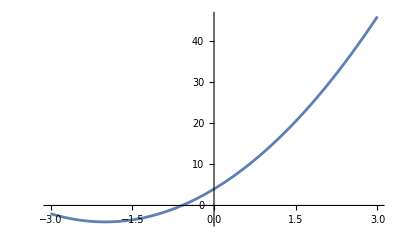

```mathematica
f = 2 x^2 + 8x + 4 
NSolve[f, x]
Plot[f ,{x, -3, 3}]
```

## Year 13 - C2

### Module 3: Statistics Normal Distribution

```mathematica
f= x^2 - 2x - (5/4.9);
NSolve[f, x]
```

{{x→-0.421411},{x→2.42141}}

WolframAlphaQueryParseResults

0.655422

```mathematica
N[CDF[NormalDistribution[0, 1], 1.9]-CDF[NormalDistribution[0, 1], -2.7]]
```

0.967816

```mathematica
1-N[CDF[NormalDistribution[24, 9], 26]]
```

0.41207

```mathematica
f=1/(√(2π))ⅇ^(-x^2/2) ;
Plot[f, {x,-3,3}]
```

(ⅇ^(-x^2/2))/(√(2 π))

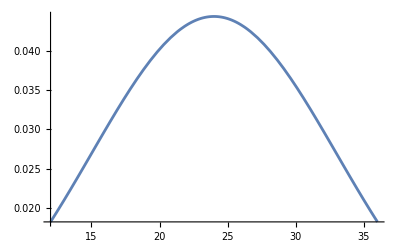

```mathematica
Plot[PDF[NormalDistribution[24,9],x],{x,12,36}]
```

```mathematica
N[CDF[NormalDistribution[24,9], 24.69]-CDF[NormalDistribution[24, 9], 24.48]]
```

0.0092888

```mathematica
N[CDF[NormalDistribution[100,16], 80]]
```

0.10565

```mathematica
n=11.2 ; 
N[CDF[NormalDistribution[100,16], 100+n]]-N[CDF[NormalDistribution[100,16], 100-n]]
```

11.2

0.516073

```mathematica
N[CDF[NormalDistribution[3.38, 2.04], 2]]
```

0.249371

```mathematica
N[CDF[NormalDistribution[3.38, 2.04], 6]]
```

0.900484

```mathematica
3.38-1.34
```

2.04

```mathematica
N[CDF[NormalDistribution[5.08, 0.0025^0.5],5]^3]
```

0.00016456

Quantile[dist, area] is calculating to the left of x,  in which the dist percentage == area size

```mathematica
dist=NormalDistribution[];
quantile=Quantile[dist, 0.25]
```

NormalDistribution[0,1]

-0.67449

mean=np
sd=sqrt(np(1-p))

```mathematica
N[CDF[NormalDistribution[20, 4], 20.5]-CDF[NormalDistribution[20, 4], 19.5]]
```

0.0994764

```mathematica
1-N[CDF[NormalDistribution[200, 160^0.5], 200.5]]
```

0.484235

```mathematica
n=100*0.025*0.975 ;
N[CDF[NormalDistribution[2.5, n^0.5], 3.5]]
```

2.4375

0.73908

```mathematica
p=1-0.6-0.025 ;
N[PDF[NormalDistribution[100 p, (100 p (1-p))^0.5], 40]]
```

0.375

0.0721188

2 x+Cos[x]

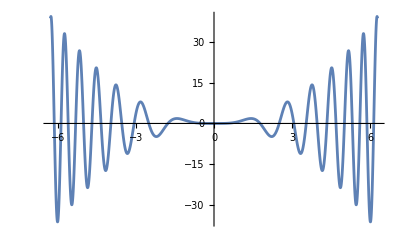
{{-Graphics-},{□}}

```mathematica
f = Sin[x] + x^2 ; 
D[f,x]
```